```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\SATHULURI\Dropbox\Quadrupeds\MPC_PID_4Bar

```mathematica
<<fourbarutils_2220.m
<<mathutils_2220.m
```

Get::noopen: Cannot open mathutils`.

Needs::nocont: Context mathutils` was not created when Needs was evaluated.

```mathematica
sol = fourBarFK[{0,0},{8,0},{4,4,4},{θ1[t],ϕ1[t],ϕ2[t]},2];
```

Set::shape: Lists {Private`solϕ2$2152,Private`f1t$2152} and Private`solveLinTrig2[{-8+4 Cos[θ1[t]]+4 Cos[ϕ1[t]]-4 Cos[ϕ2[t]],4 Sin[θ1[t]]+4 Sin[ϕ1[t]]-4 Sin[ϕ2[t]]},ϕ1[t]] are not the same shape.

ReplaceAll::reps: {Private`f1t$2152} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Union::normal: Nonatomic expression expected at position 2 in (Private`solϕ2$2152/.Private`f1t$2152)∪Private`f1t$2152.

ReplaceAll::reps: {ϕ2[t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Union::heads: Heads ϕ2 and ReplaceAll at positions 2 and 1 are expected to be the same.

```mathematica
posl1 = {l1*Cos[θ1[t]]*0.5,l1*0.5*Sin[θ1[t]]}/.sol;
posl2 = ({l1*Cos[θ1[t]],l1*Sin[θ1[t]]}+{l2*Cos[ϕ1[t]],l2*Sin[ϕ1[t]]}*0.5)/.sol;
posl3 = {8,0}+(0.5*{l1*Cos[ϕ2[t]],l1*Sin[ϕ2[t]]})/.sol;
```

ReplaceAll::reps: {(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
v1 = D[posl1,t];
v2 = D[posl2,t];
v3 = D[posl3,t];
m1 =1;
m2 = 1;
m3 = 1;
l1 = 4;
l2 =4;
l3 = 4;
g=10;
I1 = I2 = I3 = m1*16/12;
K =( v1.v1*m1+m2*v2.v2+m3*v3.v3+I1*θ1'[t]^2+I2*D[ϕ1[t]/.sol,t]^2+I3*D[ϕ2[t]/.sol,t]^2)*0.5;
P = m1*g*posl1[[2]]+m2*g*posl2[[2]]+m3*g*posl3[[2]];
e1 = D[K+P,t]
```

ReplaceAll::reps: {(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.5 (8/3 ∂_t (ϕ1[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]) ∂_{t,2} (ϕ1[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+8/3 ∂_t (ϕ2[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]) ∂_{t,2} (ϕ2[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+∂_t ({2. Cos[θ1[t]],2. Sin[θ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({2. Cos[θ1[t]],2. Sin[θ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+∂_{t,2} ({2. Cos[θ1[t]],2. Sin[θ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({2. Cos[θ1[t]],2. Sin[θ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+∂_t ({4 Cos[θ1[t]]+2. Cos[ϕ1[t]],4 Sin[θ1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({4 Cos[θ1[t]]+2. Cos[ϕ1[t]],4 Sin[θ1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+∂_{t,2} ({4 Cos[θ1[t]]+2. Cos[ϕ1[t]],4 Sin[θ1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({4 Cos[θ1[t]]+2. Cos[ϕ1[t]],4 Sin[θ1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+∂_t ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+∂_{t,2} ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+8/3 θ1'[t] θ1''[t])

```mathematica
ss=Solve[e1==0,θ1''[t]];
```

```mathematica
sa=θ1''[t]/.ss;
```

```mathematica
sn = sa/.{θ1[t]-> y1[t],θ1'[t]-> y2[t]};
```

ReplaceAll::reps: {(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
A = {y2[t],sn[[1]]}
```

{y2[t],1/y2[t]0.75 (-1.33333 ∂_t (ϕ1[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]) ∂_{t,2} (ϕ1[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-1.33333 ∂_t (ϕ2[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]) ∂_{t,2} (ϕ2[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.5 ∂_t ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.5 ∂_{t,2} ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.5 ∂_t ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.5 ∂_{t,2} ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.5 ∂_t ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.5 ∂_{t,2} ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]))}

```mathematica
Alin=D[A,{{y1[t],y2[t]}}]
```

{{0,1},{1/y2[t]0.75 (-0.5 (∂_t ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_({t,2},y1[t]) ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+∂_(t,y1[t]) ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]))-0.5 (∂_{t,2} ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_(t,y1[t]) ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+∂_({t,2},y1[t]) ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]))-0.5 (∂_t ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_({t,2},y1[t]) ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+∂_(t,y1[t]) ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]))-0.5 (∂_{t,2} ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_(t,y1[t]) ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+∂_({t,2},y1[t]) ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]))),-1/y2[t]^2 0.75 (-1.33333 ∂_t (ϕ1[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]) ∂_{t,2} (ϕ1[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-1.33333 ∂_t (ϕ2[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]) ∂_{t,2} (ϕ2[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.5 ∂_t ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.5 ∂_{t,2} ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({2. Cos[y1[t]],2. Sin[y1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.5 ∂_t ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.5 ∂_{t,2} ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({4 Cos[y1[t]]+2. Cos[ϕ1[t]],4 Sin[y1[t]]+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.5 ∂_t ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.5 ∂_{t,2} ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]))}}

```mathematica
Alin = Chop[Simplify[Alin/.{y1[t]-> π/3}]]
```

ReplaceAll::reps: {(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: π/3 is not a valid variable.

ReplaceAll::reps: {(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::ivar: π/3 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

{{0,1},{1/y2[t](-0.375 ∂_(π/3) ∂_t ({1.,1.73205}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({1.,1.73205}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.375 ∂_(π/3) ∂_{t,2} ({1.,1.73205}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({1.,1.73205}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.375 ∂_(π/3) ∂_t ({2+2. Cos[ϕ1[t]],3.4641+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({2+2. Cos[ϕ1[t]],3.4641+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.375 ∂_(π/3) ∂_{t,2} ({2+2. Cos[ϕ1[t]],3.4641+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({2+2. Cos[ϕ1[t]],3.4641+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.375 ∂_t ({1.,1.73205}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_(π/3) ∂_{t,2} ({1.,1.73205}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.375 ∂_{t,2} ({1.,1.73205}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_(π/3) ∂_t ({1.,1.73205}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.375 ∂_t ({2+2. Cos[ϕ1[t]],3.4641+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_(π/3) ∂_{t,2} ({2+2. Cos[ϕ1[t]],3.4641+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])-0.375 ∂_{t,2} ({2+2. Cos[ϕ1[t]],3.4641+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_(π/3) ∂_t ({2+2. Cos[ϕ1[t]],3.4641+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])),1/y2[t]^2(1. ∂_t (ϕ1[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]) ∂_{t,2} (ϕ1[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+1. ∂_t (ϕ2[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]) ∂_{t,2} (ϕ2[t]/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+0.375 ∂_t ({1.,1.73205}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({1.,1.73205}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+0.375 ∂_{t,2} ({1.,1.73205}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({1.,1.73205}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+0.375 ∂_t ({2+2. Cos[ϕ1[t]],3.4641+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({2+2. Cos[ϕ1[t]],3.4641+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+0.375 ∂_{t,2} ({2+2. Cos[ϕ1[t]],3.4641+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({2+2. Cos[ϕ1[t]],3.4641+2. Sin[ϕ1[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+0.375 ∂_t ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_{t,2} ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t])+0.375 ∂_{t,2} ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]).∂_t ({8+2. Cos[ϕ2[t]],2. Sin[ϕ2[t]]}/.(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]))}}

```mathematica
Final=Alin/.{y2[t]-> 0}
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

{{0,1},{ComplexInfinity,ComplexInfinity}}

```mathematica
ff =( D[ϕ1[t]/.sol,θ1[t]])/.{θ1[t]-> π/3}
```

ReplaceAll::reps: {(Private`solϕ2$2152/.ϕ2[t])∪ϕ2[t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0

```mathematica
C = -1
```

-1

```mathematica
Equball = x1''[t]-g/50*θ1[t]
```

-θ1[t]/5+x1''[t]

```mathematica
Equ = Final.{θ1[t],θ1'[t]}
```

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

{θ1'[t],Indeterminate}

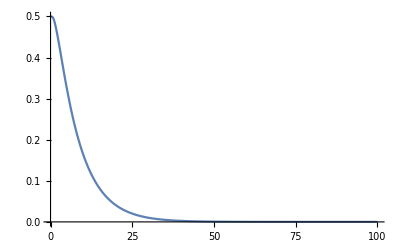

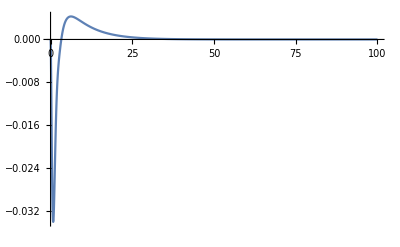

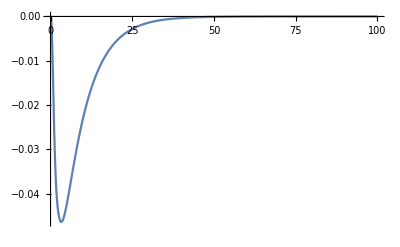

```mathematica
Kp = -1.1;
Kd =-120;
Ki = -9.9;
kc1  = 100;
kcd = -4.9;
u = Kp*yy3[t]+Kd*yy4'[t]+Ki*yy5[t]+kc1*yy1[t]+kcd*yy2[t];
tf = 100;

so=NDSolve[{yy1'[t]- yy2[t]==0,yy2'[t]-4.811252243246881 *yy1[t]-u==0,yy3'[t]-yy4[t]==0,yy4'[t]- 1*yy1[t]==0,yy5'[t]- yy1[t]==0,yy1[0]==0,yy2[0]==0,yy3[0]==0.5,yy4[0]==0,yy5[0]==0},{yy1,yy2,yy3,yy4,yy5},{t,0,tf}];
Plot[yy3[t]/.so,{t,0,tf},PlotRange->All]
Plot[yy1[t]/.so,{t,0,tf},PlotRange->All]
Plot[yy4[t]/.so,{t,0,tf},PlotRange->All]
```